```mathematica
<<MaTeX`
```

```mathematica
T[text_, magn_:1.2]:=MaTeX[text,"Preamble"->{"\\usepackage[T2A]{fontenc}", "\\usepackage{nicefrac}"},Magnification->magn]
```

```mathematica
NDSolve[2r μ'[r]ArcSin[μ[r]]==μ[r](ArcSin[μ[r]]+√(1-μ[r]^2)μ[r])&&μ[1]==1,μ,{r,0,1}]//Quiet
```

{{μ→InterpolatingFunction[…]}}

```mathematica
μ=μ/.%[[1]];
```

```mathematica
Srz[r_,x_]:=-μ[r] x;
Srr[r_,x_]:=√(1-Srz[r, x]^2)/√3
Stt[r_,x_]:=Srr[r,x]
```

```mathematica
IntSrr[r_]=Normal[1/2 Integrate[Srr[r,t],{t,-1,1}]];
```

```mathematica
α=0.1;ξ=1;C1=1;C2=2;
```

```mathematica
P[r_]:=1/α NIntegrate[μ[t],{t,r,1}]+IntSrr[r]-2/(√3)Srr[r,ξ]
```

```mathematica
Cp=With[{r=1},(√3 ArcSin[μ[r]])/μ[r]^2(1+(μ[r] √(1-μ[r]^2))/ArcSin[μ[r]]) r];
```

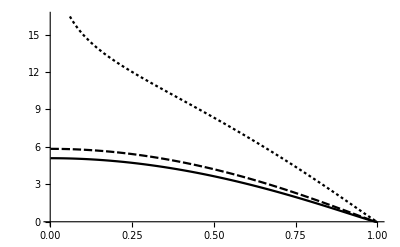

```mathematica
Plot[{P[x]-P[1],P[x]-P[1]+(3C2)/8(1-x^2),P[x]-P[1]+(3C1)/(8α)(1-x^2)-Cp Log[x]},{x,0.001,1},PlotTheme->"Monochrome",PlotLegends->{T["p^\\text{кв}"],T["p\\vert_{\\beta=2}"],T["p\\vert_{\\beta=1}"]},AxesLabel->{T["\\rho"],T["\\nicefrac{p}{\\tau_s}",1.5]}]//Quiet
```

```mathematica
Export["F:\\study_dissertation\\Russian-Phd-LaTeX-Dissertation-Template\\images\\ch1\\pressure.pdf",%]
```